%%% Zerrili equation, POLAR modes, %%% Determination of λ0[xi, ω] and s0[xi, ω] :
 %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
%%% Here, the n refers to the notation of S. Chandrasekhar, %%% n = 2, not to confuse with the "nn" used in pc - GR!

```mathematica
n=2
```

2

%%% yeh = position of the event horizon, obtained from g00 = 0, OR minimum
%%% For nn = 4 :

```mathematica
m[y]=1-27/(32 y^3)
```

1-27/(32 y^3)

```mathematica
m'[y]=FullSimplify[D[m[y],y]]
```

81/(32 y^4)

```mathematica
m''[y]=FullSimplify[D[m'[y],y]]
```

-81/(8 y^5)

```mathematica
Derivative[3][m][y]=D[m''[y],y]
```

405/(8 y^6)

```mathematica
Derivative[4][m][y]=FullSimplify[D[Derivative[3][m][y],y]]
```

-1215/(4 y^7)

%% Define yeh and Translate to xi

```mathematica
yeh=3/2
```

3/2

```mathematica
y=(3/2)/(1-xi)
```

3/(2 (1-xi))

%%% calculating the mass functions in terms of xi :

```mathematica
M[xi]=FullSimplify[1-27/(32 y^3)]
```

1+1/4 (-1+xi)^3

```mathematica
M'[xi]=81/(32 y^4)
```

1/2 (1-xi)^4

```mathematica
M''[xi]=-81/(8 y^5)
```

-4/3 (1-xi)^5

```mathematica
Derivative[3][M][xi]=405/(8 y^6)
```

40/9 (1-xi)^6

```mathematica
Derivative[4][M][xi]=-1215/(4 y^7)
```

-160/9 (1-xi)^7

%%% Potential :

```mathematica
V[xi_]=FullSimplify[((y-2 M[xi]) (18 M[xi]^3+3 y M[xi]^2 (6 n-12 M'[xi]+5 y M''[xi]-4 y^2 Derivative[3][M][xi])+y^3 (2 n^2 (1+n)-8 M'[xi]^3+M'[xi]^2 (8+6 n+3 y M''[xi])+y (M''[xi] (-n (6+n)+2 y M''[xi])+2 n y Derivative[3][M][xi])-2 M'[xi] (-4 n+y ((3+n) M''[xi]+y Derivative[3][M][xi])))+2 y^2 M[xi] (3 n^2+9 M'[xi]^2+y (M''[xi] (-3+5 n-2 y M''[xi])+(3-2 n) y Derivative[3][M][xi])+M'[xi] (-12 n+y (M''[xi]+2 y Derivative[3][M][xi])))))/(y^4 (3 M[xi]+y (n-M'[xi]))^2)]
```

-((4 (-1+xi)^2 xi^2 (6+(-4+xi) xi) (-189+xi (324+xi (-1386+xi (4148+xi (-5061+xi (-888+xi (10400+xi (-14568+xi (11145+xi (-5372+25 xi (66+(-12+xi) xi))))))))))))/(81 (-3+xi (-2+xi (6+(-4+xi) xi)))^2))

%%% xi : [0, 1]

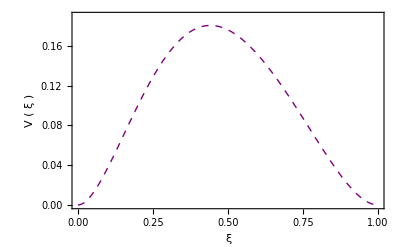

```mathematica
Plot[V[xi],{xi,0,1},Frame->True,PlotRange->{0,0.19},FrameLabel->{Style[" ξ ",Large,Black],Style[" V ( ξ ) ",Large,Black]}, PlotStyle->{{Purple, Thick, Dashed},{Purple, Thick,Dashed}}, FrameLabel->Automatic]
```

%%% factors of the differential equation, Eq. (35) :

```mathematica
F1[xi_]:=-(2/(1-xi))(1 -((1-xi)/yeh)(M[xi]-M'[xi] yeh/(1-xi))/(1- 2(1-xi)M[xi]/yeh))
```

```mathematica
F2[xi_]:=- ω^2 /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)
```

```mathematica
F3[xi_]:=-V[xi] /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)
```

%%% Factor for the - asymptotic limit :

```mathematica
Zx[xi_]:=( 1-xi)^(-2 ω) xi^{-2 ω}  ⅇ^(ω yeh/(1-xi))ⅇ^(3ω (1-xi)/(4xi))
```

%%% Ansatz for the Zerrili function, extracting Zx :

```mathematica
Z[xi_]:=Zx[xi] PP[xi]
```

%%% First derivative in xi of Z - function

```mathematica
ZDy1[xi_]:=D[Z[xi],xi]
```

%%% Second derivative of Z - function wityh respect to xi :

```mathematica
ZDy2[xi_]:=D[ZDy1[xi],xi]
```

%%% Differential equation for Z - function, Eq. (35) :

```mathematica
EQA[xi_]:= ZDy2[xi]+ F1[xi] ZDy1[xi] +( F2[xi] + F3[xi]) Z[xi]
```

%%% Extract factor of the second derivative :

```mathematica
cc0= Coefficient[EQA[xi], PP''[xi]]
```

{ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2 ω)}

%%% Divide equation by this factor :

```mathematica
EQa[xi_]:=EQA[xi]/cc0
```

%%% CHECK factor second derivative. Has to be 1 :

```mathematica
Coefficient[EQa[xi], PP''[xi]]
```

{1}

%%% Write factor of first derivative :

```mathematica
Coefficient[EQa[xi], PP'[xi]]
```

{ⅇ^(-(3 ω)/(2 (1-xi))-(3 (1-xi) ω)/(4 xi)) (1-xi)^(2 ω) xi^(2 ω) ((4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(1-2 ω))/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(2-2 ω))/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(3-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-(4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(4-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω)-3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω-4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-1-2 ω) ω+3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)}

%%% Extract factor of P[xi] :

```mathematica
Coefficient[EQa[xi], PP[xi]]
```

{ⅇ^(-(3 ω)/(2 (1-xi))-(3 (1-xi) ω)/(4 xi)) (1-xi)^(2 ω) xi^(2 ω) (-((126 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(2-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2))+(552 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(3-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(1815 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(4-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(17686 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(5-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(119657 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(6-2 ω))/(9 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(48836 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(7-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(8527 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(8-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(25846 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(9-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(152075 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(10-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(164120 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(11-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(360835 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(12-2 ω))/(9 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(63406 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(13-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(24359 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(14-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(6724 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(15-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(425 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(16-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)-(50 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(17-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+(25 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(18-2 ω))/(9 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2 (-3+xi (-2+xi (6+(-4+xi) xi)))^2)+3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-3-2 ω) ω+3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2-2 ω) ω+2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω-(3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(12 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(12 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(2-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(2-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(29 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(2-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(3-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(32 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(3-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(3-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-(2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(4-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(4-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω-(2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+9/16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-4-2 ω) ω^2+3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-3-2 ω) ω^2-9/4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2-2 ω) ω^2-3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2-2 ω) ω^2+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω^2-6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-1-2 ω) ω^2-8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω^2+9/4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(-2 ω) ω^2-(9 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(-2 ω) ω^2)/(4 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(-2 ω) ω^2+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω^2)}

%%% λ0[y_,om_]:=FullSimplify[Coefficient[EQa[y], PP'[y]]],

```mathematica
FullSimplify[Coefficient[EQa[xi], PP'[xi]]]
```

{((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)}

TAKE AN EXTRA MINUS SIGN IN ORDER TO RELATE TO THE AIM EQUATIONS!

```mathematica
λ0[xi_,ω_]:=-(((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2))
```

```mathematica
λ0[xi,ω]
```

-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)

%%% s0[y_,  om_] := FullSimplify[Coefficient[EQa[y], PP[y]]]

```mathematica
Simplify[Coefficient[EQa[xi], PP[xi]]]
```

{(xi^4 (-773504+793208 ω-1122911 ω^2)+16 xi^14 (25-20 ω+16 ω^2)-324 (56+167 ω^2)-432 xi (-100-167 ω+263 ω^2)-16 xi^13 (400-331 ω+278 ω^2)+xi^12 (48000-41064 ω+36185 ω^2)+6 xi^3 (82016-53164 ω+36191 ω^2)+9 xi^2 (-17424-9488 ω+36641 ω^2)-2 xi^11 (110176-97468 ω+89925 ω^2)-16 xi^7 (129896-131273 ω+129451 ω^2)+4 xi^5 (76256-91988 ω+215631 ω^2)-4 xi^9 (365520-346348 ω+344805 ω^2)+xi^10 (680528-622896 ω+599277 ω^2)+xi^6 (974256-988064 ω+715454 ω^2)+xi^8 (2168672-2126672 ω+2155398 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2 (-3-2 xi+6 xi^2-4 xi^3+xi^4)^2)}

%%% Copy result and multiply with (-1), %%% because it is shifted to the right side of the equation :

```mathematica
s0[xi_,ω_]:=-((xi^4 (-773504+793208 ω-1122911 ω^2)+16 xi^14 (25-20 ω+16 ω^2)-324 (56+167 ω^2)-432 xi (-100-167 ω+263 ω^2)-16 xi^13 (400-331 ω+278 ω^2)+xi^12 (48000-41064 ω+36185 ω^2)+6 xi^3 (82016-53164 ω+36191 ω^2)+9 xi^2 (-17424-9488 ω+36641 ω^2)-2 xi^11 (110176-97468 ω+89925 ω^2)-16 xi^7 (129896-131273 ω+129451 ω^2)+4 xi^5 (76256-91988 ω+215631 ω^2)-4 xi^9 (365520-346348 ω+344805 ω^2)+xi^10 (680528-622896 ω+599277 ω^2)+xi^6 (974256-988064 ω+715454 ω^2)+xi^8 (2168672-2126672 ω+2155398 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2 (-3-2 xi+6 xi^2-4 xi^3+xi^4)^2))
```

%%% copy results for s0 and λ0 :

```mathematica
s0[xi,ω]
```

-((xi^4 (-773504+793208 ω-1122911 ω^2)+16 xi^14 (25-20 ω+16 ω^2)-324 (56+167 ω^2)-432 xi (-100-167 ω+263 ω^2)-16 xi^13 (400-331 ω+278 ω^2)+xi^12 (48000-41064 ω+36185 ω^2)+6 xi^3 (82016-53164 ω+36191 ω^2)+9 xi^2 (-17424-9488 ω+36641 ω^2)-2 xi^11 (110176-97468 ω+89925 ω^2)-16 xi^7 (129896-131273 ω+129451 ω^2)+4 xi^5 (76256-91988 ω+215631 ω^2)-4 xi^9 (365520-346348 ω+344805 ω^2)+xi^10 (680528-622896 ω+599277 ω^2)+xi^6 (974256-988064 ω+715454 ω^2)+xi^8 (2168672-2126672 ω+2155398 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2 (-3-2 xi+6 xi^2-4 xi^3+xi^4)^2))

```mathematica
λ0[xi, ω]
```

-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)